```mathematica
SetDirectory["G:\\My Drive\\Projects\\FourierDisplay\\Software"];
LoadPack:=Get["G:\\My Drive\\Projects\\FourierDisplay\\Software\\FourierPack.wl"];
LoadPack;
```

## FourierDisplay - ImaginaryCoefficients

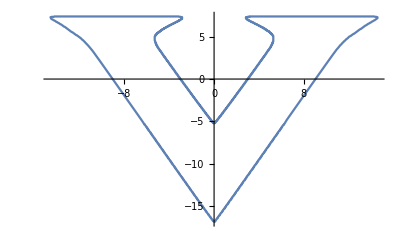

```mathematica
points = LineData["VirginiaV"]; 
ListLinePlot[points]
```

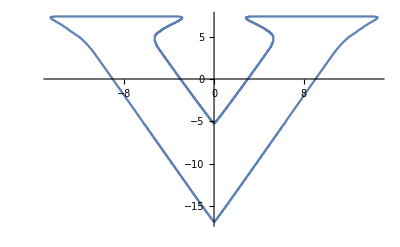

```mathematica
tour = MakeTour[points]; (*Reorder points to form a continuous path*)
ListLinePlot[tour]
```

### EuclidianDistance Parametrization

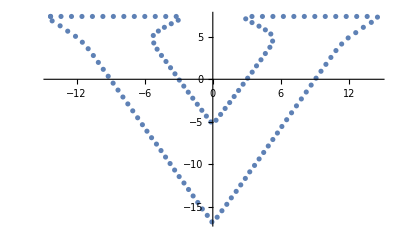

```mathematica
sample = UniformResample[PrependIndices[points, "ParametrizationType"->"EuclidianDistance"],100, "ParametrizationType"->"Given"];
(*By sampling from data indexed by distance along path, we get an even distribution of points along the line.  The "Given" option for UniformResample attaches the distance indices to sample["SamplePointsIndexed"]*)
coefFunc = CnFFT[MakeComplex[sample["SamplePoints"]]];
ListPlot[sample["SamplePoints"]]
```

```mathematica
funcs= Function[t,#]&/@Table[ApproxFunction[coefFunc,t,Length@sample["SamplePoints"],n, "Scale"->sample["Length"]]["Function"],{n,1,Length@sample["SamplePoints"]/2,10}];
```

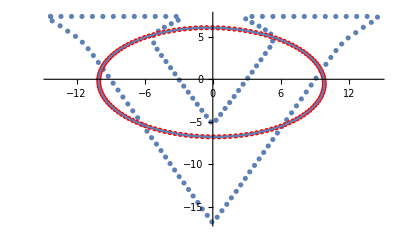
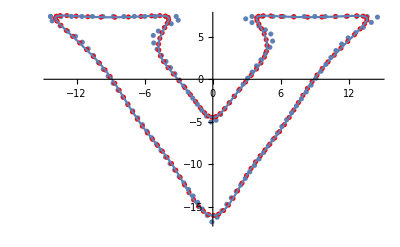
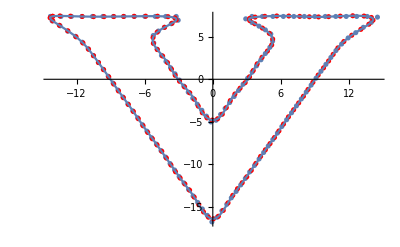
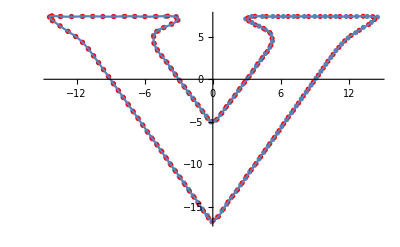
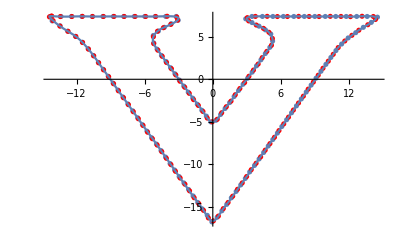
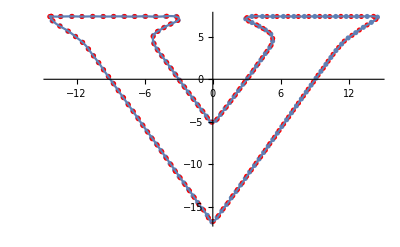
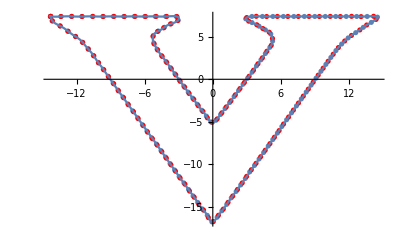
{35.1323
-Graphics-,0.346206
-Graphics-,0.26105
-Graphics-,0.255154
-Graphics-,0.254411
-Graphics-,0.254446
-Graphics-,0.254741
-Graphics-}

```mathematica
With[{l2 =L2Error[sample["SamplePointsIndexed"], #, "Complex"]}, Column[{l2["L2Error"],Show[
ListPlot[sample["SamplePoints"]],
ListPlot[l2["ApproxPoints"],PlotStyle->Red], 
ParametricPlot[{Re@#, Im@#}&@#[t],{t,0,sample["Length"]}]]}]]&/@funcs
```

### Linear Parametrization

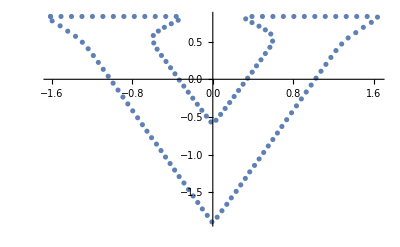

```mathematica
sample = UniformResample[PrependIndices[points, "ParametrizationType"->"EuclidianDistance"],100, "ParametrizationType"->"Linear"];
(*Resample with distance along path parametrization, but attach 'linear' (ie 0-N) indices in sample["SamplePointsIndexed"]*)
coefFunc = CnFFT[MakeComplex[sample["SamplePoints"]]];
ListPlot[sample["SamplePoints"]]
```

```mathematica
funcs= Function[t,#]&/@Table[ApproxFunction[coefFunc,t,Length@sample["SamplePoints"],n, "Scale"->Default]["Function"],{n,1,Length@sample["SamplePoints"]/2,10}];
```

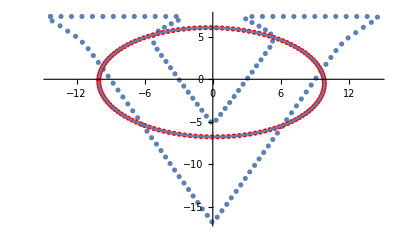
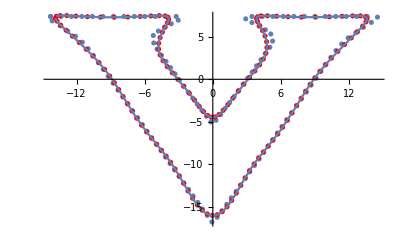
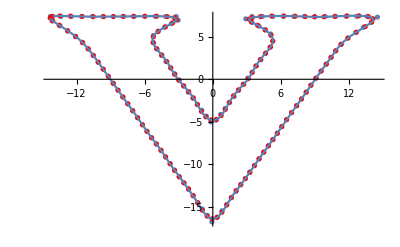
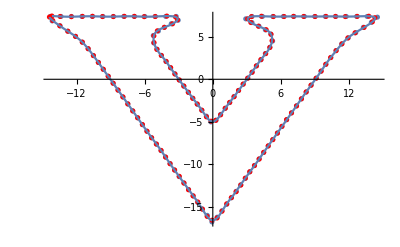
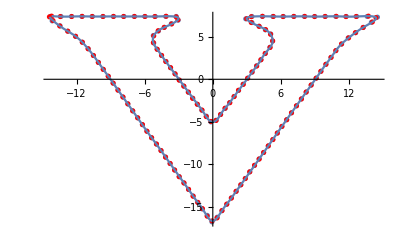
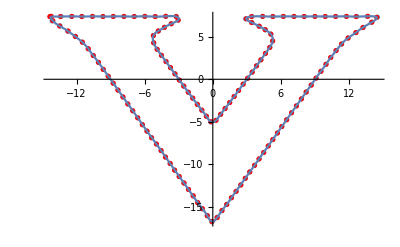
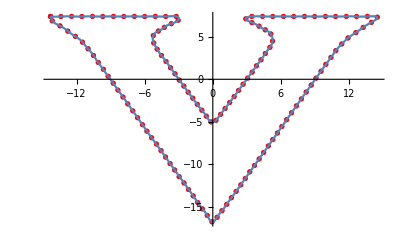
{35.018
-Graphics-,0.102551
-Graphics-,0.0110189
-Graphics-,0.00327915
-Graphics-,0.00154515
-Graphics-,0.000690443
-Graphics-,0.000156545
-Graphics-}

```mathematica
With[{l2 =L2Error[sample["SamplePointsIndexed"], #, "Complex"]}, Column[{l2["L2Error"],Show[
ListPlot[sample["SamplePoints"]],
ListPlot[l2["ApproxPoints"],PlotStyle->Red], 
ParametricPlot[{Re@#, Im@#}&@#[t],{t,0,sample["Length"]}]]}]]&/@funcs
```

## Circles and Visualization

```mathematica
Manipulate[Module[{func, N=n},
func =ReIm@ApproxFunction[coefFunc,t,Length@sample["SamplePoints"],N]["Function"];
ParametricPlot[func,{t,0,sample["Length"]}]],{n}]
```

```mathematica
circleObject = ApproxFunction[coefFunc,t,Length@sample["SamplePoints"],5 ,"Sort"->True];
```

```mathematica
EpicyclePlot[circleObject,{t,0,sample["Length"]},"Frames"->100, "Movie"->True]
```

EpicyclePlot[<|Coefficients→{-0.111981-0.353221 ⅈ,-1.75747-0.0001097 ⅈ,-8.17849+0.441397 ⅈ,-0.345899+3.33022 ⅈ,0.392412+4.4123 ⅈ,-0.458032-0.112664 ⅈ,-1.11563+0.083815 ⅈ,0.112069-0.913703 ⅈ,-0.0246047-0.160341 ⅈ,-0.814779-0.130747 ⅈ,-0.596158+0.130502 ⅈ},Radii→{0.370547,1.75747,8.19039,3.34814,4.42972,0.471684,1.11877,0.92055,0.162218,0.825203,0.610275},Speeds→{0.,-0.0490874,0.0490874,-0.0981748,0.0981748,-0.147262,0.147262,-0.19635,0.19635,-0.245437,0.245437},Terms→{-0.111981-0.353221 ⅈ,(-1.75747-0.0001097 ⅈ) ⅇ^((0.+0.0490874 ⅈ) t),(-8.17849+0.441397 ⅈ) ⅇ^((0.-0.0490874 ⅈ) t),(-0.345899+3.33022 ⅈ) ⅇ^((0.+0.0981748 ⅈ) t),(0.392412+4.4123 ⅈ) ⅇ^((0.-0.0981748 ⅈ) t),(-0.458032-0.112664 ⅈ) ⅇ^((0.+0.147262 ⅈ) t),(-1.11563+0.083815 ⅈ) ⅇ^((0.-0.147262 ⅈ) t),(0.112069-0.913703 ⅈ) ⅇ^((0.+0.19635 ⅈ) t),(-0.0246047-0.160341 ⅈ) ⅇ^((0.-0.19635 ⅈ) t),(-0.814779-0.130747 ⅈ) ⅇ^((0.+0.245437 ⅈ) t),(-0.596158+0.130502 ⅈ) ⅇ^((0.-0.245437 ⅈ) t)},ArmEnds→{-0.111981-0.353221 ⅈ,(-0.111981-0.353221 ⅈ)-(1.75747+0.0001097 ⅈ) ⅇ^((0.+0.0490874 ⅈ) t),(-0.111981-0.353221 ⅈ)-(8.17849-0.441397 ⅈ) ⅇ^((0.-0.0490874 ⅈ) t)-(1.75747+0.0001097 ⅈ) ⅇ^((0.+0.0490874 ⅈ) t),(-0.111981-0.353221 ⅈ)-(8.17849-0.441397 ⅈ) ⅇ^((0.-0.0490874 ⅈ) t)-(1.75747+0.0001097 ⅈ) ⅇ^((0.+0.0490874 ⅈ) t)-(0.345899-3.33022 ⅈ) ⅇ^((0.+0.0981748 ⅈ) t),(-0.111981-0.353221 ⅈ)-(8.17849-0.441397 ⅈ) ⅇ^((0.-0.0490874 ⅈ) t)-(1.75747+0.0001097 ⅈ) ⅇ^((0.+0.0490874 ⅈ) t)+(0.392412+4.4123 ⅈ) ⅇ^((0.-0.0981748 ⅈ) t)-(0.345899-3.33022 ⅈ) ⅇ^((0.+0.0981748 ⅈ) t),(-0.111981-0.353221 ⅈ)-(8.17849-0.441397 ⅈ) ⅇ^((0.-0.0490874 ⅈ) t)-(1.75747+0.0001097 ⅈ) ⅇ^((0.+0.0490874 ⅈ) t)+(0.392412+4.4123 ⅈ) ⅇ^((0.-0.0981748 ⅈ) t)-(0.345899-3.33022 ⅈ) ⅇ^((0.+0.0981748 ⅈ) t)-(0.458032+0.112664 ⅈ) ⅇ^((0.+0.147262 ⅈ) t),(-0.111981-0.353221 ⅈ)-(8.17849-0.441397 ⅈ) ⅇ^((0.-0.0490874 ⅈ) t)-(1.75747+0.0001097 ⅈ) ⅇ^((0.+0.0490874 ⅈ) t)+(0.392412+4.4123 ⅈ) ⅇ^((0.-0.0981748 ⅈ) t)-(0.345899-3.33022 ⅈ) ⅇ^((0.+0.0981748 ⅈ) t)-(1.11563-0.083815 ⅈ) ⅇ^((0.-0.147262 ⅈ) t)-(0.458032+0.112664 ⅈ) ⅇ^((0.+0.147262 ⅈ) t),(-0.111981-0.353221 ⅈ)-(8.17849-0.441397 ⅈ) ⅇ^((0.-0.0490874 ⅈ) t)-(1.75747+0.0001097 ⅈ) ⅇ^((0.+0.0490874 ⅈ) t)+(0.392412+4.4123 ⅈ) ⅇ^((0.-0.0981748 ⅈ) t)-(0.345899-3.33022 ⅈ) ⅇ^((0.+0.0981748 ⅈ) t)-(1.11563-0.083815 ⅈ) ⅇ^((0.-0.147262 ⅈ) t)-(0.458032+0.112664 ⅈ) ⅇ^((0.+0.147262 ⅈ) t)+(0.112069-0.913703 ⅈ) ⅇ^((0.+0.19635 ⅈ) t),(-0.111981-0.353221 ⅈ)-(8.17849-0.441397 ⅈ) ⅇ^((0.-0.0490874 ⅈ) t)-(1.75747+0.0001097 ⅈ) ⅇ^((0.+0.0490874 ⅈ) t)+(0.392412+4.4123 ⅈ) ⅇ^((0.-0.0981748 ⅈ) t)-(0.345899-3.33022 ⅈ) ⅇ^((0.+0.0981748 ⅈ) t)-(1.11563-0.083815 ⅈ) ⅇ^((0.-0.147262 ⅈ) t)-(0.458032+0.112664 ⅈ) ⅇ^((0.+0.147262 ⅈ) t)-(0.0246047+0.160341 ⅈ) ⅇ^((0.-0.19635 ⅈ) t)+(0.112069-0.913703 ⅈ) ⅇ^((0.+0.19635 ⅈ) t),(-0.111981-0.353221 ⅈ)-(8.17849-0.441397 ⅈ) ⅇ^((0.-0.0490874 ⅈ) t)-(1.75747+0.0001097 ⅈ) ⅇ^((0.+0.0490874 ⅈ) t)+(0.392412+4.4123 ⅈ) ⅇ^((0.-0.0981748 ⅈ) t)-(0.345899-3.33022 ⅈ) ⅇ^((0.+0.0981748 ⅈ) t)-(1.11563-0.083815 ⅈ) ⅇ^((0.-0.147262 ⅈ) t)-(0.458032+0.112664 ⅈ) ⅇ^((0.+0.147262 ⅈ) t)-(0.0246047+0.160341 ⅈ) ⅇ^((0.-0.19635 ⅈ) t)+(0.112069-0.913703 ⅈ) ⅇ^((0.+0.19635 ⅈ) t)-(0.814779+0.130747 ⅈ) ⅇ^((0.+0.245437 ⅈ) t),(-0.111981-0.353221 ⅈ)-(8.17849-0.441397 ⅈ) ⅇ^((0.-0.0490874 ⅈ) t)-(1.75747+0.0001097 ⅈ) ⅇ^((0.+0.0490874 ⅈ) t)+(0.392412+4.4123 ⅈ) ⅇ^((0.-0.0981748 ⅈ) t)-(0.345899-3.33022 ⅈ) ⅇ^((0.+0.0981748 ⅈ) t)-(1.11563-0.083815 ⅈ) ⅇ^((0.-0.147262 ⅈ) t)-(0.458032+0.112664 ⅈ) ⅇ^((0.+0.147262 ⅈ) t)-(0.0246047+0.160341 ⅈ) ⅇ^((0.-0.19635 ⅈ) t)+(0.112069-0.913703 ⅈ) ⅇ^((0.+0.19635 ⅈ) t)-(0.596158-0.130502 ⅈ) ⅇ^((0.-0.245437 ⅈ) t)-(0.814779+0.130747 ⅈ) ⅇ^((0.+0.245437 ⅈ) t)},Centers→{0,-0.111981-0.353221 ⅈ,(-0.111981-0.353221 ⅈ)-(1.75747+0.0001097 ⅈ) ⅇ^((0.+0.0490874 ⅈ) t),(-0.111981-0.353221 ⅈ)-(8.17849-0.441397 ⅈ) ⅇ^((0.-0.0490874 ⅈ) t)-(1.75747+0.0001097 ⅈ) ⅇ^((0.+0.0490874 ⅈ) t),(-0.111981-0.353221 ⅈ)-(8.17849-0.441397 ⅈ) ⅇ^((0.-0.0490874 ⅈ) t)-(1.75747+0.0001097 ⅈ) ⅇ^((0.+0.0490874 ⅈ) t)-(0.345899-3.33022 ⅈ) ⅇ^((0.+0.0981748 ⅈ) t),(-0.111981-0.353221 ⅈ)-(8.17849-0.441397 ⅈ) ⅇ^((0.-0.0490874 ⅈ) t)-(1.75747+0.0001097 ⅈ) ⅇ^((0.+0.0490874 ⅈ) t)+(0.392412+4.4123 ⅈ) ⅇ^((0.-0.0981748 ⅈ) t)-(0.345899-3.33022 ⅈ) ⅇ^((0.+0.0981748 ⅈ) t),(-0.111981-0.353221 ⅈ)-(8.17849-0.441397 ⅈ) ⅇ^((0.-0.0490874 ⅈ) t)-(1.75747+0.0001097 ⅈ) ⅇ^((0.+0.0490874 ⅈ) t)+(0.392412+4.4123 ⅈ) ⅇ^((0.-0.0981748 ⅈ) t)-(0.345899-3.33022 ⅈ) ⅇ^((0.+0.0981748 ⅈ) t)-(0.458032+0.112664 ⅈ) ⅇ^((0.+0.147262 ⅈ) t),(-0.111981-0.353221 ⅈ)-(8.17849-0.441397 ⅈ) ⅇ^((0.-0.0490874 ⅈ) t)-(1.75747+0.0001097 ⅈ) ⅇ^((0.+0.0490874 ⅈ) t)+(0.392412+4.4123 ⅈ) ⅇ^((0.-0.0981748 ⅈ) t)-(0.345899-3.33022 ⅈ) ⅇ^((0.+0.0981748 ⅈ) t)-(1.11563-0.083815 ⅈ) ⅇ^((0.-0.147262 ⅈ) t)-(0.458032+0.112664 ⅈ) ⅇ^((0.+0.147262 ⅈ) t),(-0.111981-0.353221 ⅈ)-(8.17849-0.441397 ⅈ) ⅇ^((0.-0.0490874 ⅈ) t)-(1.75747+0.0001097 ⅈ) ⅇ^((0.+0.0490874 ⅈ) t)+(0.392412+4.4123 ⅈ) ⅇ^((0.-0.0981748 ⅈ) t)-(0.345899-3.33022 ⅈ) ⅇ^((0.+0.0981748 ⅈ) t)-(1.11563-0.083815 ⅈ) ⅇ^((0.-0.147262 ⅈ) t)-(0.458032+0.112664 ⅈ) ⅇ^((0.+0.147262 ⅈ) t)+(0.112069-0.913703 ⅈ) ⅇ^((0.+0.19635 ⅈ) t),(-0.111981-0.353221 ⅈ)-(8.17849-0.441397 ⅈ) ⅇ^((0.-0.0490874 ⅈ) t)-(1.75747+0.0001097 ⅈ) ⅇ^((0.+0.0490874 ⅈ) t)+(0.392412+4.4123 ⅈ) ⅇ^((0.-0.0981748 ⅈ) t)-(0.345899-3.33022 ⅈ) ⅇ^((0.+0.0981748 ⅈ) t)-(1.11563-0.083815 ⅈ) ⅇ^((0.-0.147262 ⅈ) t)-(0.458032+0.112664 ⅈ) ⅇ^((0.+0.147262 ⅈ) t)-(0.0246047+0.160341 ⅈ) ⅇ^((0.-0.19635 ⅈ) t)+(0.112069-0.913703 ⅈ) ⅇ^((0.+0.19635 ⅈ) t),(-0.111981-0.353221 ⅈ)-(8.17849-0.441397 ⅈ) ⅇ^((0.-0.0490874 ⅈ) t)-(1.75747+0.0001097 ⅈ) ⅇ^((0.+0.0490874 ⅈ) t)+(0.392412+4.4123 ⅈ) ⅇ^((0.-0.0981748 ⅈ) t)-(0.345899-3.33022 ⅈ) ⅇ^((0.+0.0981748 ⅈ) t)-(1.11563-0.083815 ⅈ) ⅇ^((0.-0.147262 ⅈ) t)-(0.458032+0.112664 ⅈ) ⅇ^((0.+0.147262 ⅈ) t)-(0.0246047+0.160341 ⅈ) ⅇ^((0.-0.19635 ⅈ) t)+(0.112069-0.913703 ⅈ) ⅇ^((0.+0.19635 ⅈ) t)-(0.814779+0.130747 ⅈ) ⅇ^((0.+0.245437 ⅈ) t)},Function→(-0.111981-0.353221 ⅈ)-(8.17849-0.441397 ⅈ) ⅇ^((0.-0.0490874 ⅈ) t)-(1.75747+0.0001097 ⅈ) ⅇ^((0.+0.0490874 ⅈ) t)+(0.392412+4.4123 ⅈ) ⅇ^((0.-0.0981748 ⅈ) t)-(0.345899-3.33022 ⅈ) ⅇ^((0.+0.0981748 ⅈ) t)-(1.11563-0.083815 ⅈ) ⅇ^((0.-0.147262 ⅈ) t)-(0.458032+0.112664 ⅈ) ⅇ^((0.+0.147262 ⅈ) t)-(0.0246047+0.160341 ⅈ) ⅇ^((0.-0.19635 ⅈ) t)+(0.112069-0.913703 ⅈ) ⅇ^((0.+0.19635 ⅈ) t)-(0.596158-0.130502 ⅈ) ⅇ^((0.-0.245437 ⅈ) t)-(0.814779+0.130747 ⅈ) ⅇ^((0.+0.245437 ⅈ) t)|>,{t,0,127},Frames→100,Movie→True]

## Sorted Coefficients

```mathematica
(*Take the largest 10 coefficients by ABS*)
```

```mathematica
Module[{coefObject = CnFFT[MakeComplex[sample["SamplePoints"]], 50], circleObject},
circleObject = ApproxFunction[coefObject["CoefficientFunction"],t,Length@sample["SamplePoints"],coefObject["CoefficientList"], "Sort"->False];
EpicyclePlot[circleObject,{t,0,sample["Length"]},"Frames"->50, "Movie"->True]]
```

EpicyclePlot[1]
 |  |  |  |